```mathematica
nestedSine[n_,x_]:=Module[{sine=Sin[x],sign=1,s=2*Sin[x]},Table[sign*=-1;s+=sign*sine;sine=Sin[sine];,{i,2,n+1}];
s]
nestedNSine[n_,x_]:=nestedSine[n,nestedSine[n,x]]
```

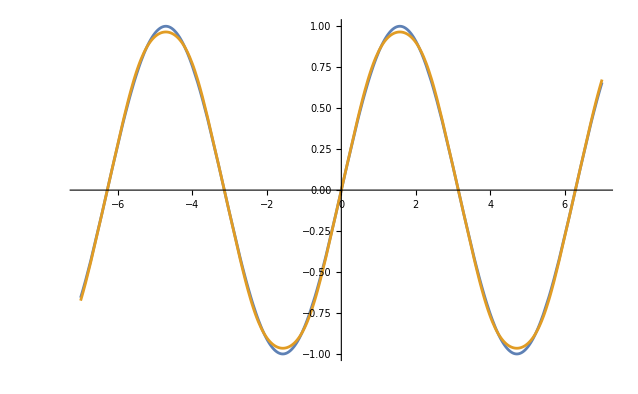

```mathematica
Plot[{Sin[x],nestedNSine[3, x]}, {x, -7,7}]
```

```mathematica
error[func_]:=NIntegrate[(Sin[x]-func[x])^2, {x, -2Pi, 2Pi}]
```

```mathematica
seriesSum[coefs_,x_]:=Module[{sine=Sin[x],s=0},Table[s+=coefs[[i]]*sine;sine=Sin[sine];,{i,Length[coefs]}];
s]
seriesSum[coefs_][x_]:=Module[{sine=Sin[x],s=0},Table[s+=coefs[[i]]*sine;sine=Sin[sine];,{i,Length[coefs]}];
s]
```

```mathematica
coefs=Table[a[i], {i, 1, 10}]
sol=NMinimize[error[seriesSum[coefs][seriesSum[coefs][#]]&], coefs, Method->"NelderMead"]
```

{a[1],a[2],a[3],a[4],a[5],a[6],a[7],a[8],a[9],a[10]}

NIntegrate::inumr: The integrand («1»)^2 has evaluated to non-numerical values for all sampling points in the region with boundaries {{-6.28319,0.}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

NIntegrate::inumr: The integrand («1»)^2 has evaluated to non-numerical values for all sampling points in the region with boundaries {{-6.28319,0.}}.

{1.52392×10^-6,{a[1]→-3.61897,a[2]→6.22319,a[3]→-1.9878,a[4]→-2.85394,a[5]→-1.28695,a[6]→-0.222112,a[7]→2.18777,a[8]→2.64449,a[9]→0.0929135,a[10]→-2.17973}}

```mathematica
sol
```

{1.52392×10^-6,{a[1]→-3.61897,a[2]→6.22319,a[3]→-1.9878,a[4]→-2.85394,a[5]→-1.28695,a[6]→-0.222112,a[7]→2.18777,a[8]→2.64449,a[9]→0.0929135,a[10]→-2.17973}}

```mathematica
bestFunc=seriesSum[Values[Last@sol]]
```

seriesSum[{-3.61897,6.22319,-1.9878,-2.85394,-1.28695,-0.222112,2.18777,2.64449,0.0929135,-2.17973}]

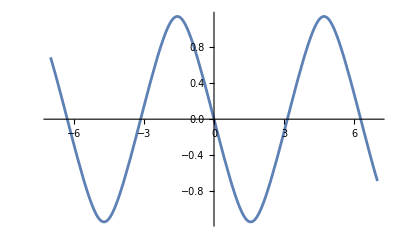

```mathematica
Plot[bestFunc[x], {x, -7,7}]
```

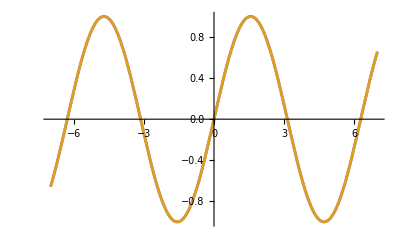

```mathematica
Plot[{Sin[x],bestFunc[bestFunc[x]]}, {x, -7,7}]
```

```mathematica
StringReplace[ToString[bestFunc/@Subdivide[-7,7, 1000-1]//InputForm], {"`"->"", "{"->"[", "}"->"]"}]//CopyToClipboard
```